## How much we can use Ratio

```mathematica
Needs["MaTeX`"]
```

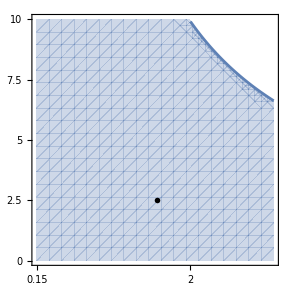

```mathematica
plot1=Show[RegionPlot[h(0.10 r +0.0019)<=0.002,{r,0.15,3},{h,0,0.01},ImageSize->{290,250},LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},FrameLabel->{{MaTeX["\\Large \\text{Rest Leg Length, $L_0$ (mm)}"],None},{MaTeX["\\LARGE \\text{$\\ell_\\text{d}$}"],None}},FrameTicks->{{{{0,0},{0.0025,2.5},{0.005,5},{0.0075,7.5},{0.01,10}},Automatic},{{{0.15,0.15},{1,1},{2,2},{3,3},{0.05,0.05}},Automatic}},Epilog->Text[Style[MaTeX["\\normalsize \\text{$L_0(0.10 \\ell_\\text{d}+0.0019)\\leq2 \\,\\text{mm}$}"],15,FontFamily->"Latin Modern Roman 10"],{1.6,0.0025}],BoundaryStyle->None],
Plot[0.002/(0.10 r +0.0019),{r,2,3}]]
```

## Influence of y speed

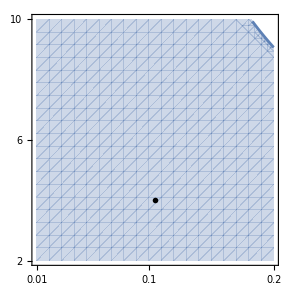

```mathematica
plot3=Show[RegionPlot[h(11.22 y - 0.039)<=0.02,{y,0.01,0.2},{h,0.002,0.01},LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},FrameLabel->{{MaTeX["\\Large \\text{Rest Leg Length, $L_0$ (mm)}"],None},{MaTeX["\\LARGE \\text{$\\dot{y}_0$}"],None}},ImageSize->{290,250},FrameTicks->{{{{0.002,2},{0.006,6},{0.01,10}},Automatic},{{{0.01,0.01},{0.1,0.1},{0.2,0.2}},Automatic}},BoundaryStyle->None],
Graphics[Text[Style[MaTeX["\\normalsize \\text{$L_0(11.22\\dot{y}_0-0.039)\\leq20\\,\\text{mm}$}"],15],{0.105,0.004}]],
Plot[0.02/(11.22 r -0.039),{r,0.183,0.2}]

]
```

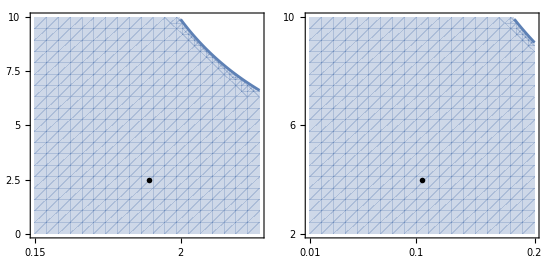

```mathematica
plot=Show[GraphicsGrid[{{plot1,plot3}},ImageSize->{550,260},Spacings->{Scaled[0],Scaled[0]}],
Graphics[{Text[Style["a",17,FontFamily->"Latin Modern Roman 10"],{40,15}],
Text[Style["b",17,FontFamily->"Latin Modern Roman 10"],{330,15}]
}]

]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\selectingparameters1.pdf",plot]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\selectingparameters1.pdf